```mathematica
a=1;
```

```mathematica
b=2;
```

```mathematica
c=a+b
```

3

```mathematica
π
```

π

```mathematica
N[π,1]
```

3.

# Funktionen :

-beginnen immer mit einem großen Buchstben
-Argumente von Funktionen immer in eckigen Klammern

```mathematica
Sin[2π]
```

0

```mathematica
N[%]
```

0.

```mathematica
Sin[2]//N
```

0.909297

```mathematica
Clear[a,b,c]
```

```mathematica
funktion[x_]:=a x^2-b x-c
```

-c-b x+a x^2

```mathematica
funktion[3]
```

9 a-3 b-c

```mathematica
a=1;
b=2;
c=4;
funktion[3]
```

-1

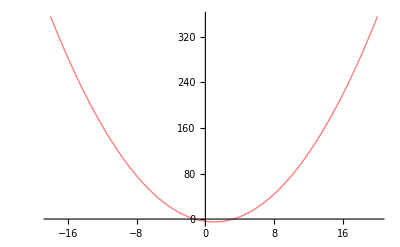

```mathematica
Plot[funktion[x],{x,-18,20},PlotStyle->{Pink}]
```

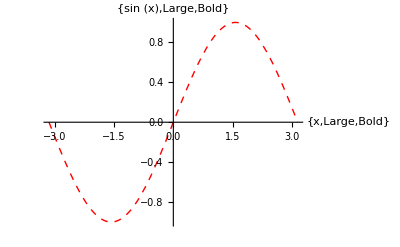

```mathematica
Plot[Sin[x],{x,-π,π},PlotStyle->{Red,Dashed},AxesLabel->{Style[{"x",Large,Bold}],Style[{"sin (x)",Large,Bold}]}]
```

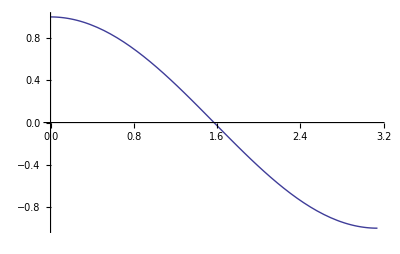

```mathematica
ParametricPlot[{t,Cos[t]},{t,0,π}]
```

```mathematica
g[x_,y_]=Sin[x]+Sin[y]
```

Sin[x]+Sin[y]

```mathematica
g[π,2π]
```

0

```mathematica
Plot3D[g[x,y],{x,-π,π},{y,-π,π}]
```

-Graphics3D-

## Differemzieren und Integrieren

```mathematica
D[funktion[x],x]
```

-2+2 x

```mathematica
D[g[x,y],y]
```

Cos[y]

```mathematica
Integrate[funktion[x],{x,0,3}]
```

-12

```mathematica
Plot[Integrate[funktion[x],{x,0,e}],{e,0,5}]
```

$Aborted

## Lösen von Gleichungssystemen bzw. Gleichungen

```mathematica
nullstellen=Solve[funktion[x]==0,x]
```

{{x→1-√5},{x→1+√5}}

```mathematica
Reduce[funktion[x]==0,x][[2]]
```

x==1+√5

```mathematica
ReplaceAll[funktion[x],nullstellen[[1]]]
```

-4-2 (1-√5)+(1-√5)^2

```mathematica
Simplify[%]
```

0

```mathematica
funktion[x]/.nullstellen[[2]]
```

-4-2 (1+√5)+(1+√5)^2

```mathematica
funktion[x]/.nullstellen
```

{-4-2 (1-√5)+(1-√5)^2,-4-2 (1+√5)+(1+√5)^2}

```mathematica
Solve[{x+y==2,x^2-y+s==4},{x,y}]
```

{{x→1/2 (-1-√(25-4 s)),y→1/2 (5+√(25-4 s))},{x→1/2 (-1+√(25-4 s)),y→1/2 (5-√(25-4 s))}}

```mathematica
%//Simplify
```

{{x→1/2 (-1-√(25-4 s)),y→1/2 (5+√(25-4 s))},{x→1/2 (-1+√(25-4 s)),y→1/2 (5-√(25-4 s))}}

```mathematica
Simplify[Sqrt[4 n^2]]
```

2 √(n^2)

```mathematica
$Assumpions={n>0,j ∈ Reals}$
```

{$ (n>0),$ (j∈Reals)}

## Listen

```mathematica
y1=Table[x,{x,1,4}];
v2=Table[{x,x^3},{x,10,100}];
```

```mathematica
y1.v2
```

134

```mathematica
Table[Table[x^2+3y,{x,0,10}],{y,0,10}];
```

```mathematica
TraditionalForm[%]
```

(0 | 1 | 4 | 9 | 16 | 25 | 36 | 49 | 64 | 81 | 100
3 | 4 | 7 | 12 | 19 | 28 | 39 | 52 | 67 | 84 | 103
6 | 7 | 10 | 15 | 22 | 31 | 42 | 55 | 70 | 87 | 106
9 | 10 | 13 | 18 | 25 | 34 | 45 | 58 | 73 | 90 | 109
12 | 13 | 16 | 21 | 28 | 37 | 48 | 61 | 76 | 93 | 112
15 | 16 | 19 | 24 | 31 | 40 | 51 | 64 | 79 | 96 | 115
18 | 19 | 22 | 27 | 34 | 43 | 54 | 67 | 82 | 99 | 118
21 | 22 | 25 | 30 | 37 | 46 | 57 | 70 | 85 | 102 | 121
24 | 25 | 28 | 33 | 40 | 49 | 60 | 73 | 88 | 105 | 124
27 | 28 | 31 | 36 | 43 | 52 | 63 | 76 | 91 | 108 | 127
30 | 31 | 34 | 39 | 46 | 55 | 66 | 79 | 94 | 111 | 130)

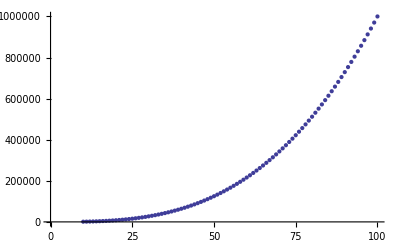

```mathematica
ListPlot[v2]
```

```mathematica
v2[[5;;50]]
```

{{14,2744},{15,3375},{16,4096},{17,4913},{18,5832},{19,6859},{20,8000},{21,9261},{22,10648},{23,12167},{24,13824},{25,15625},{26,17576},{27,19683},{28,21952},{29,24389},{30,27000},{31,29791},{32,32768},{33,35937},{34,39304},{35,42875},{36,46656},{37,50653},{38,54872},{39,59319},{40,64000},{41,68921},{42,74088},{43,79507},{44,85184},{45,91125},{46,97336},{47,103823},{48,110592},{49,117649},{50,125000},{51,132651},{52,140608},{53,148877},{54,157464},{55,166375},{56,175616},{57,185193},{58,195112},{59,205379}}

## Schleifen

```mathematica
c=Table[0,{6}];
For[i=0,i≤5,i++,
c[[i]]=3-i;
Print[i]];
```

0

1

2

3

4

5

```mathematica
c
```

3[2,1,0,-1,-2,0]

```mathematica
For[i=1,i≤5,i++,
k=3 i-2;
If[k<10,Print[k],Print[i]]]
```

1

4

7

4

5

## Die Novikov - Maschine

```mathematica
Clear["Global`*"]
```

```mathematica
p=Table[0,{2}];
```

```mathematica
P[Tih_]:=kN*(Th-Tih);
dP[Tih_]=D[P[Tih],Tih];
f[Tih_]:=kF*(1/Tih-1/Th);
df[Tih_]=D[s[Tih],Tih];
s[Tih_]:=kS*(Th^4-Tih^4);
ds[Tih_]=D[s[Tih],Tih];
DP[Tih_]:=kDP*(Th-Tih)^1.25;
dDP[Tih_]=D[DP[Tih],Tih];
```

```mathematica
kN=10;
kF=10^6;
kDP=4;
kS=10^(-7);
Th=350;
Tl=200;
```

{{t→-100 √7},{t→100 √7}}

```mathematica
ddP[Tih_]=D[dP[Tih],Tih]
```

-(400 (350-Tih))/Tih^3-400/Tih^2

```mathematica
Simplify[ddP[-√Th √Tl]]
```

1/(50 √7)

Newton

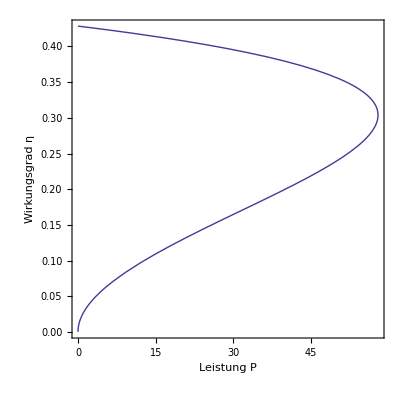

```mathematica
PN[Tih_]:=P[Tih]-P[Tih]*Tl/Tih;
η[Tih_]:=PN[Tih]/P[Tih];
ParametricPlot[{PN[t],η[t]},{t,Tl,Th},AspectRatio->1,Frame->True,FrameStyle->Directive[15,"cmr10"],FrameLabel->{Style["Leistung P",Italic,"cmr10",15],Style["Wirkungsgrad η",Italic,"cmr10",15]}]
```

Fourier

{{t→0},{t→0},{t→0}}

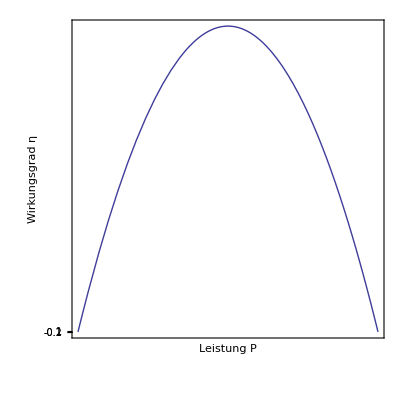

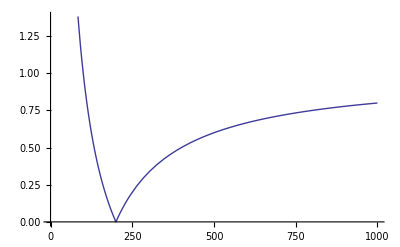

```mathematica
result=Solve[df[t]==0,t]
PF[x_]=f[x]-f[x]*Tl/x;
ηF[x_]:=Abs[PF[x]]/Abs[f[x]];
ParametricPlot[{ηF[t],PF[t]},{t,Tl,Th},AspectRatio->1,Ticks->{{π,-π},{-.1,-0.2,1}},Frame->True,FrameStyle->Directive[15,"cmr10"],FrameLabel->{Style["Leistung P",Italic,"cmr10",15],Style["Wirkungsgrad η",Italic,"cmr10",15]}]
Plot[{ηF[x]},{x,0,1000}]
```

Strahlung

{{t→0},{t→0},{t→0}}

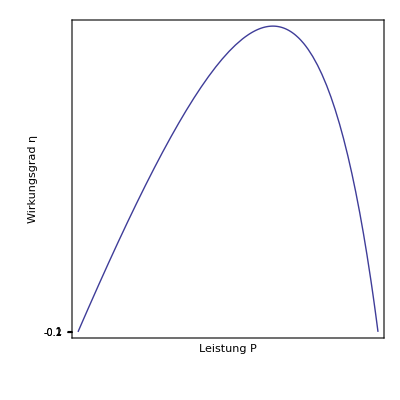

```mathematica
result=Solve[ds[t]==0,t]
PS[x_]=s[x]-s[x]*Tl/x;
ηs[x_]:=PS[x]/s[x];
ParametricPlot[{ηs[t],PS[t]},{t,Tl,Th},AspectRatio->1,Ticks->{{π,-π},{-.1,-0.2,1}},Frame->True,FrameStyle->Directive[15,"cmr10"],FrameLabel->{Style["Leistung P",Italic,"cmr10",15],Style["Wirkungsgrad η",Italic,"cmr10",15]}]
```

Dulong - Petit

{{t→350.}}

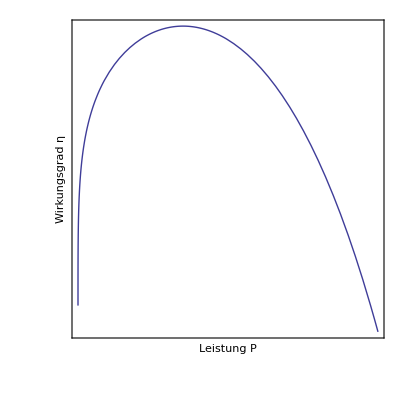

```mathematica
result=Solve[dDP[t]==0,t]
PDP[x_]:=DP[x]-DP[x]*Tl/x;
ηDP[x_]:=Abs[PDP[x]]/Abs[s[x]];
ParametricPlot[{DP[t]/2100,ηDP[t]},{t,Tl,Th},AspectRatio->1,Ticks->{{π,-π},{-.1,-0.2,1}},Frame->True,FrameStyle->Directive[15,"cmr10"],FrameLabel->{Style["Leistung P",Italic,"cmr10",15],Style["Wirkungsgrad η",Italic,"cmr10",15]}]
```

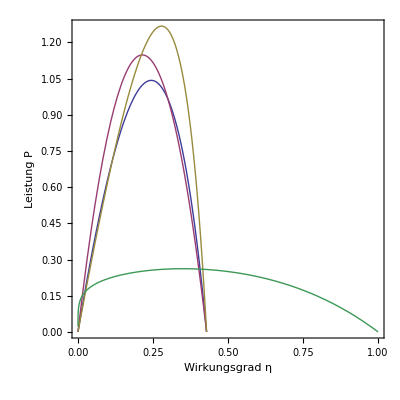

```mathematica
ParametricPlot[{{η[t],PN[t]/200},{ηF[t],PF[t]/200},{ηs[t],PS[t]/200},{DP[t]/2100,ηDP[t]}},{t,Tl,Th},AspectRatio->1,Frame->True,FrameStyle->Directive[15,"cmr10"],FrameLabel->{Style["Wirkungsgrad η",Italic,"cmr10",15],Style["Leistung P",Italic,"cmr10",15]}]
```

```mathematica
ql[kl_]=kl*(Th-Tl);
η[Tih_,kl_]:=PN[Tih]/(P[Tih]+ql[kl]);
ηF[x_,kl_]:=Abs[PF[x]]/Abs[f[x]+ql[kl]];
ηs[x_,kl_]:=PS[x]/(s[x]+ql[kl]);
ηDP[x_,kl_]:=PDP[x]/(DP[x]+ql[kl]);
```

```mathematica
Animate[ParametricPlot[{{η[t,kl],PN[t]/250},{ηF[t,kl],PF[t]/250},{ηs[t,kl],PS[t]/250},{DP[t]/2100,ηDP[t,kl]}},{t,Tl,Th},AspectRatio->1,Frame->True,PlotRange->All,FrameStyle->Directive[15,"cmr10"],FrameLabel->{Style["Wirkungsgrad η",Italic,"cmr10",15],Style["Leistung P",Italic,"cmr10",15]}],{kl,-1,10,0.0001}]
```

Curzon - Ahlborn

```mathematica
Th=350;
Tl=200;
k=10;
kN=10;
Q[Tih_]:=kN*(Th-Tih);
PN[Tih_]:=Q[Tih]-Q[Tih]*Tl/Tih;
η[Tih_]:=PN[Tih]/Q[Tih];
Til[Tih_]:=Th*Tl/Tih;
qh[Tih_]:=k(Th-Tih);
ql[Tih_]:=k*(Til[Tih]-Tl);
Pl[Tih_]:=k/Tih*(Th*(Tih-Tl)-Tih^2+Tl*Tih);
ηl[Tih_]:=P[Tih]/(qh[Tih]+ql[Tih]);
```

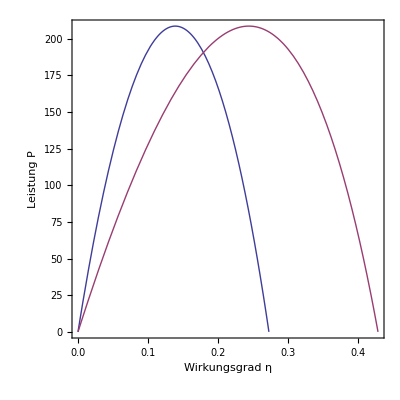

```mathematica
ParametricPlot[{{ηl[t],Pl[t]},{η[t],PN[t]}},{t,Tl,Th},AspectRatio->1,Frame->True,FrameStyle->Directive[15,"cmr10"],FrameLabel->{Style["Wirkungsgrad η",Italic,"cmr10",15],Style["Leistung P",Italic,"cmr10",15]}]
```

```mathematica
FullSimplify[k(th-tih-th/tih-tl)]
```

10 (th-th/tih-tih-tl)

## Kochsche Kurve

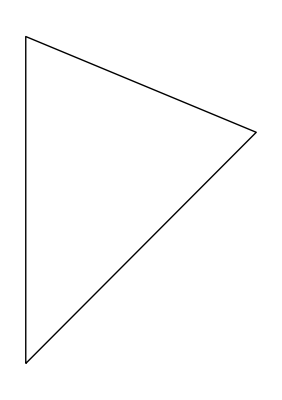

```mathematica
Graphics[
{
Line[{{0,0},{0,1},{1/Sqrt[2],1/Sqrt[2]},{0,0}}]}]
```

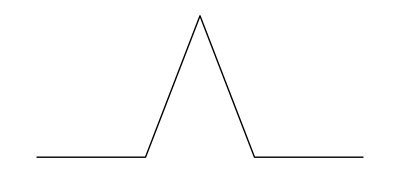

```mathematica
Graphics[
{
Line[{{0,0},{1/3,0},{0.5,Sqrt[3]/4},{2/3,0},{1,0}}]}]
```